```mathematica
randomCards[nDiscoveredCards_Integer]:=Module[{output="",output2="",p1,p2,b1,b2,b3,b4,b5,ArrayCheck,nplayer},
p1=RandomInteger[{1,52}];
ArrayCheck=Table[p1,{1}];
p2=RandomInteger[{1,52}];
While[MemberQ[ArrayCheck,p2],p2=RandomInteger[{1,52}]];
AppendTo[ArrayCheck,p2];
nplayer=nDiscoveredCards;
While[MemberQ[ArrayCheck,p2],p2=RandomInteger[{1,52}]];
If[nplayer>=1,b1=RandomInteger[{1,52}];
While[MemberQ[ArrayCheck,b1],b1=RandomInteger[{1,52}]],b1=0];
AppendTo[ArrayCheck,b1];
If[nplayer>=2,b2=RandomInteger[{1,52}];
While[MemberQ[ArrayCheck,b2],b2=RandomInteger[{1,52}]],b2=0];
AppendTo[ArrayCheck,b2];
If[nplayer>=3,b3=RandomInteger[{1,52}];
While[MemberQ[ArrayCheck,b3],b3=RandomInteger[{1,52}]],b3=0];
AppendTo[ArrayCheck,b3];
If[nplayer>=4,b4=RandomInteger[{1,52}];
While[MemberQ[ArrayCheck,b4],b4=RandomInteger[{1,52}]],b4=0];
AppendTo[ArrayCheck,b4];
If[nplayer>=5,b5=RandomInteger[{1,52}];
While[MemberQ[ArrayCheck,b5],b5=RandomInteger[{1,52}]],b5=0];
AppendTo[ArrayCheck,b5];
output=Row[{ResourceFunction["PlayingCardGraphic"][b1],ResourceFunction["PlayingCardGraphic"][b2],ResourceFunction["PlayingCardGraphic"][b3],ResourceFunction["PlayingCardGraphic"][b4],ResourceFunction["PlayingCardGraphic"][b5]},Spacer[10]];
output2=Rasterize@ResourceFunction["PlayingCardGraphic"][{p1,p2}];
{output,output2}]
```

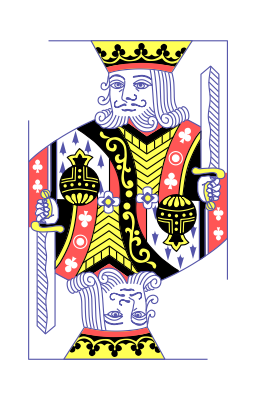
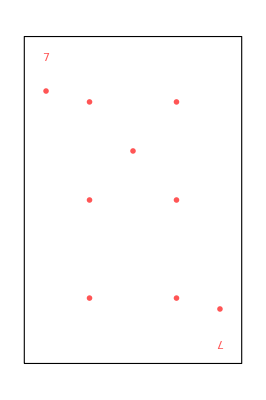
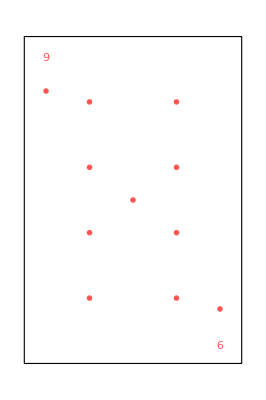
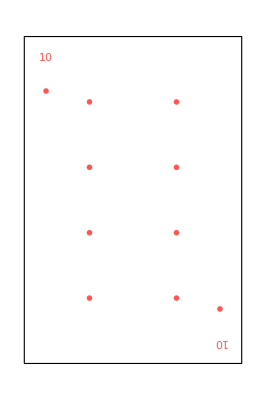
-Graphics--Graphics--Graphics--Graphics--Graphics-

-Graphics-

```mathematica
{output, output2}= randomCards[5];
output
output2
```